```mathematica
Y[ud_]:= Ex*ud^2  /2;
```

```mathematica
gama[u_]:=gama0 ( Tanh[u/c +d] -Tanh[d]);
```

```mathematica
D[gama[u],u]
```

Sech[0.1+u]^2

```mathematica
D[(gama0 Sech[d+u/c]^2)/c,u]
```

-2 Sech[0.1+u]^2 Tanh[0.1+u]

```mathematica
jump[ep_]:=c(ArcCosh[Sqrt[gama0/(c ep Ex)]]-d)
```

```mathematica
c=1; Ex=1; d=0.1; gama0=1;
```

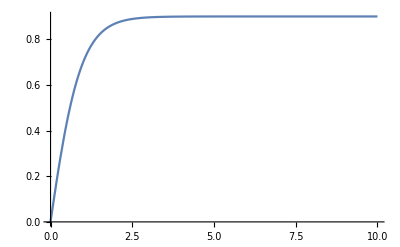

```mathematica
Plot[gama[u], {u,0,10}, PlotRange -> All]
```

```mathematica
epm= gama0/(c Ex Cosh[d]^2)
```

0.990066

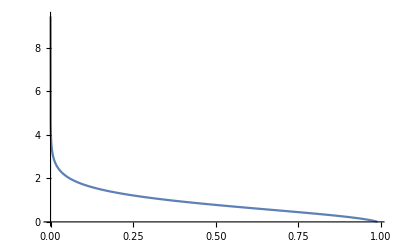

```mathematica
Plot[jump[ep],{ep,0,epm}, PlotRange->All]
```

```mathematica
lc= (Ex c^2)/(2 gama0 Tanh[d] Sech[d]^2)
```

5.06699

```mathematica
jump[epm]
```

-9.57567×10^-16

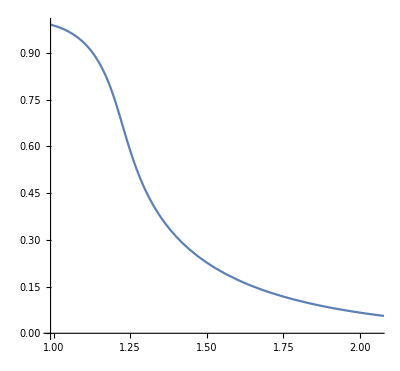

```mathematica
graph1=ParametricPlot[{sigma/Ex + jump[sigma/Ex], sigma},{sigma,0.01,epm}]
```

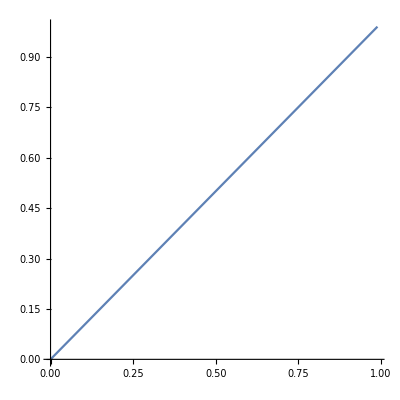

```mathematica
graph2=ParametricPlot[{sigma/Ex,sigma},{sigma,0,epm}]
```

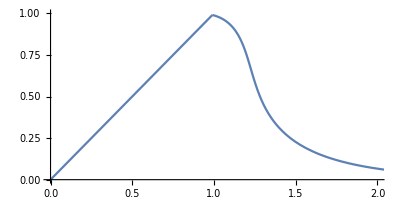

```mathematica
Show[graph1,graph2,AxesOrigin -> {0,0}, PlotRange-> {{0,2},{0,1}}]
```

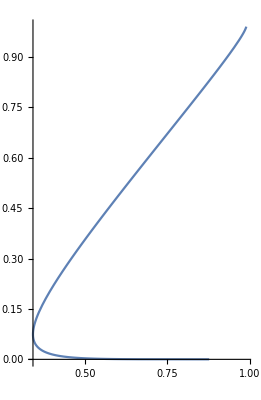

```mathematica
graph3=ParametricPlot[{sigma/Ex +1/7 jump[sigma/Ex],sigma}, { sigma,0,epm}]
```

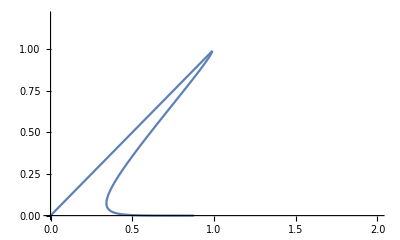

```mathematica
Show[graph2,graph3, AxesOrigin -> {0,0}, PlotRange-> {{0,2},{0,1.2}}]
```